```mathematica
transmission:=transmission=Monitor[Table[{x,Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_device_50_length_100_up_"<>ToString[x]<>"_.dat"]},{x,Range[10,60,10]}],x]
```

```mathematica
transmission[[2]][[2]][[;;,2]]
```

{0.422329,0.515154,0.317544,0.225667,0.208597,0.14312,0.129521,0.105556,0.150366,0.297375,0.17599,0.236777,0.363598,0.163863,0.370272,0.607457,0.407228,0.50985,0.376129,0.489527,0.499648,0.332795,0.44033,0.445199,0.441983,0.378904,0.624213,0.370833,0.808763,0.773138,0.698873,1.01436,0.911168,1.00365,1.00082,1.1439,0.954874,1.1071,0.806411,0.913425,0.72039,0.818322,0.961285,1.33532,1.51804,1.62227,1.78089,1.88481,1.81593,1.93052,1.97562,1.92907,1.92324,1.94505,1.96849,1.8394,1.86603,1.74645,1.60575,1.51129,1.19149,1.40383,1.25877,1.26644,1.27224,1.45605,1.74929,1.56995,1.85311,2.07352,2.51065,2.70093,2.7845,2.80835,2.94744,2.92686,2.99946,3.12377,3.1191,3.06122,3.12321,2.99695,3.13685,3.03946,2.48655,2.31907,3.05985,3.28703,3.52529,3.71303,3.74665,3.87193,3.97281,3.93338,4.09105,3.99526,2.98587,3.50308,3.86904,3.87397,3.98189,4.25,4.24658,4.43863,4.55451,4.61475,4.65146,4.42157,4.25618,4.15989,4.16282,4.19064,4.20656,4.25514,4.29437,4.33332,4.37857,4.3933,4.41947,4.37025,4.22833,4.14084,4.0885,4.10136,4.10843,4.09999,4.13044,4.12623,4.14655,4.14534,4.12139,4.06845,3.94241,3.79009,3.63412,3.57131,3.4364,3.29509,3.05899,2.38115,2.83482,3.1342,3.32911,3.45949,3.55018,3.56905,3.59723,3.64628,3.67,3.74057,3.7625,3.80164,3.84963,3.88817,3.90692,3.90929,3.87528,3.82017,3.78135,3.75785,3.80623,3.78979,3.81349,3.80002,3.80829,3.81273,3.79418,3.76473,3.71414,3.59708,3.5373,3.49819,3.42074,3.36074,3.28642,3.12621,2.80525,2.39282,2.68699,2.81732,2.90262,2.93754,2.98323,3.05194,3.11074,3.13908,3.18387,3.22585,3.27071,3.29315,3.28207,3.25845,3.21332,3.21435,3.19862,3.22132,3.22854,3.23635,3.26239,3.25939,3.26065}

```mathematica
input = Table[Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/example_30_"<>ToString[x]<>"_.dat"],{x,1,100}]
```

{{{0.,0.936587},{0.01,0.413872},{0.02,0.0289796},{0.03,0.0388835},{0.04,0.0904264},{0.05,0.0543994},{0.06,0.154988},{0.07,0.0558198},{0.08,0.0800385},{0.09,0.248292},{0.1,0.0892904},{0.11,0.161097},{0.12,0.343453},175,{1.88,3.19984},{1.89,2.98079},{1.9,3.58763},{1.91,3.44855},{1.92,3.40049},{1.93,3.43581},{1.94,3.20742},{1.95,2.91019},{1.96,2.94257},{1.97,2.99137},{1.98,3.20051},{1.99,2.90495},{2.,2.9162}},98,{1}}
 |  |  |  |

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[{transmission[[vvv,1]],Module[{B1=Transpose[{m5[[1;;201]][[;;,1]],Abs[(m5[[1;;201,2]]-transmission[[vvv]][[2]][[;;,2]])]^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{vvv,6}];
list=ρ1;{list,list[[Position[list,Min[list]][[1,1]]]][[1]]}]
```

```mathematica
Show[ListLinePlot[Monitor[Table[Import["~/PhD_new/PhD/fwi/AGNR/sudo_q/new_total_100_lead_15_device_50_length_100_up_"<>ToString[x]<>"_.dat"],{x,Range[10,60,10]}],x]],ListLinePlot[input[[2]],PlotStyle->Black]]
```

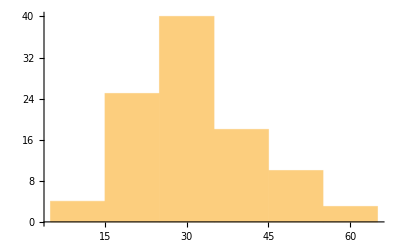

```mathematica
Table[misfit[2,1.5,n][[2]],{n,100}]//Histogram
```

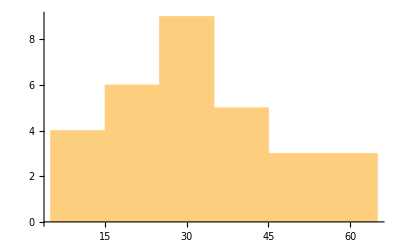

```mathematica
Histogram[{20,30,10,20,30,60,10,30,40,30,30,30,10,50,40,30,40,50,60,30,10,40,40,30,20,60,50,20,20,20}]
```

```mathematica
Table[Table[{x,Interpolation[misfit[2,1.2,n][[1]]][x]},{x,10,60}][[Position[Table[{x,Interpolation[misfit[2,1.2,n][[1]]][x]},{x,10,60}],Min[Table[{x,Interpolation[misfit[2,1.2,n][[1]]][x]},{x,10,60}]]][[1,1]]]],{n,100}]
```

{{19,0.00145478},{58,0.00777489},{26,0.00232104},{27,0.00215395},{51,0.00224129},{52,0.00514296},{25,0.00155772},{34,0.00254007},{20,0.0014522},{20,0.00123892},{47,0.00302936},{37,0.00258702},{20,0.0021572},{20,0.00113946},{36,0.00252607},{17,0.00174123},{35,0.00230388},{60,0.00724644},{42,0.00270209},{23,0.00158584},{11,0.00133577},{23,0.00151875},{29,0.00280031},{20,0.00179839},{28,0.0024139},{24,0.00166149},{44,0.00535828},{24,0.00233309},{21,0.00199322},{19,0.00151365},{31,0.00286749},{23,0.00119145},{30,0.00191171},{26,0.00184224},{24,0.00117066},{48,0.00506928},{41,0.00257733},{20,0.00162605},{33,0.00228557},{20,0.00168882},{34,0.00198431},{29,0.00159256},{36,0.00196939},{21,0.00136353},{21,0.00163131},{29,0.00337452},{23,0.00137226},{23,0.00239829},{12,0.00114371},{27,0.00122742},{43,0.00319752},{23,0.00139256},{26,0.00138904},{60,0.00527804},{27,0.00175431},{26,0.00193624},{29,0.00143994},{34,0.0021818},{37,0.0031181},{28,0.00187168},{57,0.00502304},{29,0.00217589},{32,0.00191436},{21,0.00155208},{23,0.00187485},{45,0.00341222},{48,0.00358678},{49,0.00415227},{27,0.00212188},{35,0.00176793},{24,0.00285364},{21,0.00186802},{32,0.00191954},{24,0.00181107},{26,0.00140222},{27,0.00189425},{23,0.00167547},{57,0.00439981},{34,0.00275972},{28,0.00205341},{54,0.00288636},{29,0.00309025},{19,0.00167436},{34,0.00185222},{25,0.0017663},{23,0.00126341},{24,0.00142705},{32,0.00306697},{30,0.00144931},{50,0.00586781},{19,0.00138683},{40,0.00276464},{40,0.003142},{28,0.00172235},{24,0.00135999},{30,0.00645217},{23,0.00231562},{27,0.00172502},{36,0.00268782},{60,0.00570073}}

```mathematica
Transpose[%97][[1]]-30
```

{-11,28,-4,-3,21,22,-5,4,-10,-10,17,7,-10,-10,6,-13,5,30,12,-7,-19,-7,-1,-10,-2,-6,14,-6,-9,-11,1,-7,0,-4,-6,18,11,-10,3,-10,4,-1,6,-9,-9,-1,-7,-7,-18,-3,13,-7,-4,30,-3,-4,-1,4,7,-2,27,-1,2,-9,-7,15,18,19,-3,5,-6,-9,2,-6,-4,-3,-7,27,4,-2,24,-1,-11,4,-5,-7,-6,2,0,20,-11,10,10,-2,-6,0,-7,-3,6,30}

```mathematica
Mean[%98]
```

21/20

```mathematica
N[21/20]
```

1.05

```mathematica
[RandomVariate[NormalDistribution[1.05,11.38],5000]]
```

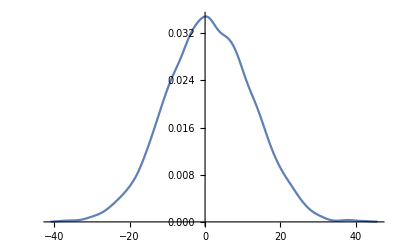

```mathematica
SmoothHistogram[%110]
```

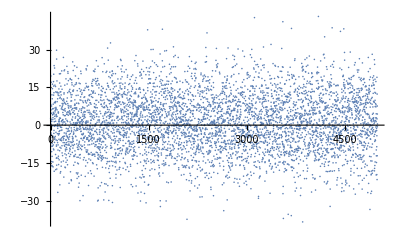

```mathematica
ListPlot[%110]
```

```mathematica
CDF[NormalDistribution[1.05,11.38],x]
```

1/2 Erfc[0.0621359 (1.05-x)]

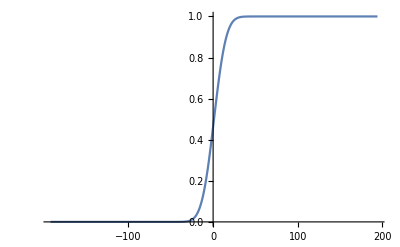

```mathematica
Plot[1/2 Erfc[0.06213592101815004 (1.05-x)],{x,-192.07500407766986,194.17500407766988}]
```

```mathematica
PDF[NormalDistribution[1.05,11.38],x]
```

0.0350564 ⅇ^(-0.00386087 (-1.05+x)^2)

```mathematica
StandardDeviation[%98]
```

(√(17113/33))/2

```mathematica
N[(√(17113/33))/2]
```

11.3861

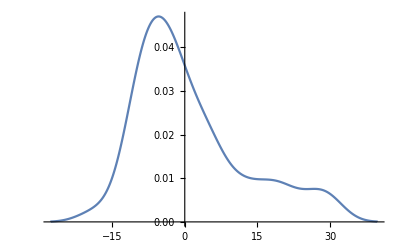

```mathematica
SmoothHistogram[%98]
```

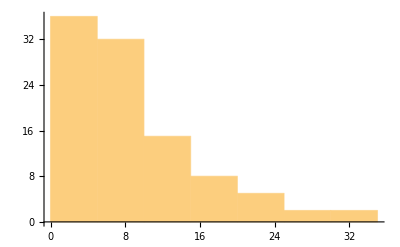

```mathematica
Histogram[%93]
```

```mathematica
N[829/3000]
```

0.276333

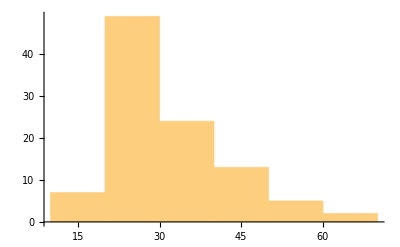

```mathematica
Histogram[%87]
```

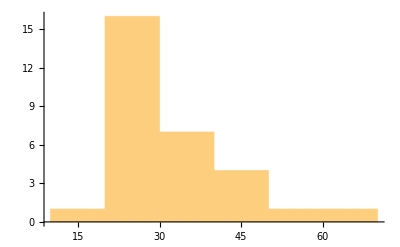

```mathematica
Histogram[{22,60,24,24,46,48,22,37,23,27,42,30,20,28,36,22,36,57,39,24,10,28,32,22,20,36,49,21,24,24}]
```

```mathematica
Abs[Transpose[%60][[1]]-30]/30//Mean
```

283/900

```mathematica
N[283/900]
```

0.314444

```mathematica
N[241/1000]
```

0.241

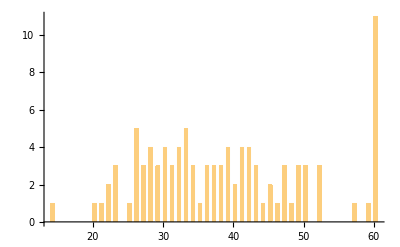

```mathematica
Histogram[%49,{0.5}]
```

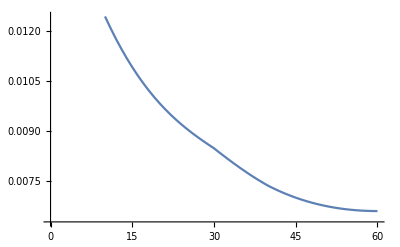

```mathematica
ListPlot[%40,Joined->True]
```

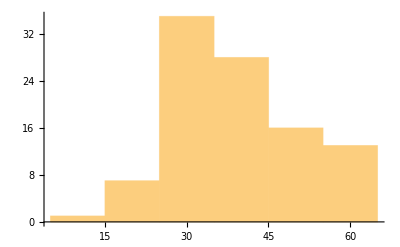

```mathematica
Table[misfit[2,1.5,n][[2]],{n,100}]//Histogram
```

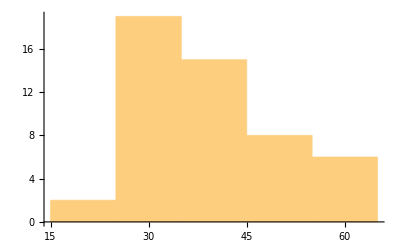

```mathematica
Histogram[{60,50,40,50,40,20,30,30,40,30,40,60,40,30,30,50,30,40,40,30,40,40,50,50,60,30,40,30,50,30,30,30,40,40,30,30,50,40,40,60,30,40,50,30,30,30,60,20,60,30}]
```